# The Edge of Random Tensor Eigenvalues with Deviation: Compilation of codes

```mathematica
Quit[];
```

## 1. Analytical expressions

### Signed distribution

```mathematica
Uabz[a_,b_,z_]:=Gamma[b-1]/Gamma[a] z^(1-b)Hypergeometric1F1[a-b+1,2-b,z]+Gamma[1-b]/Gamma[a-b+1] Hypergeometric1F1[a,b,z];
```

```mathematica
DZperp[L_,v_,α_]:=(3α/(2 v^2))^(1-L/2) D[k Uabz[1-L/2,3/2,3α k^2/(2 v^2)],k]/.k->1
```

```mathematica
Zperp[L_,v_,α_]:=(3α/(2 v^2))^(1-L/2) k Uabz[1-L/2,3/2,3α k^2/(2 v^2)]/.k->1
```

```mathematica
volSphere[L_]:=2 Pi^((L+1)/2)/Gamma[(L+1)/2]
```

```mathematica
eS0[v_,b_,L_,α_]:=Exp[-α v^2/(v^4+4 α b)]/Sqrt[(3 v^4+12 α b)(v^4+12 α b)^(L-1)]
```

```mathematica
rhoS[v_,b_,L_,α_]:=-((v^4-4 α b)/(v^4+4α b)Zperp[L,v,α]+8b v^2/(v^4+12 α b)DZperp[L,v,α])eS0[v,b,L,α]
```

```mathematica
rhoRadial[v_,b_,L_,α_]:=rhoS[v,b,L,α] volSphere[L-1]Abs[v]^(L-1) Sqrt[12 Pi α]^L/(2 Pi )^L
```

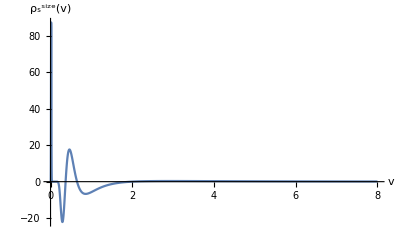

```mathematica
Lval=7;
beta=0.001/Lval^2;
analytPlotSigned=Plot[rhoRadial[v,beta,Lval,1/2],{v,0,8},PlotRange->All,AxesLabel->{Style["v",16],Style["ρ_s^size(v)",16]}]
```

### Genuine distribution: Naoki’s code

```mathematica
al=1/2; (* This is Auffinger et al.'s normalization, it cannot be changed.*)

Clear[p,x,v,g,s,f,rho,coeff,aln,part]

p[j_,v_]:=(2^j j! Sqrt[Pi])^(-1/2) HermiteH[j,v] Exp[-v^2/2];

g[n_]:=1/2(-Integrate[p[n,t],{t,v,Infinity},Assumptions->v>0]+Integrate[p[n,t],{t,-Infinity,v},Assumptions->v>0]);

s[n_]:=Sum[p[i,v]^2,{i,0,n-1}];

aln[n_]:=Which[Mod[n,2]==0,0,True,
m=(n-1)/2;
p[2m,v]/Integrate[p[2m,t],{t,-Infinity,Infinity}]
]

f[n_]:=(s[n]+(n/2)^(1/2) p[n-1,v] g[n]+aln[n])/Sqrt[n];

Clear[rhod];
q=3;

(* ABC result *)
rhod[n_]:=2 Sqrt[n]/v^2(q-1)^((n-1)/2) Exp[-(q-2)/(4 (q-1) v^2)] (f[n]/. v->-y*Sqrt[3/(2*2)]/. y->1/v);


Clear[gam1,gam2,gam3,L];

q11=Sqrt[4x-1]/(2 Sqrt[eps] x)-1/(2x);
q12=-1/(2x)+Sqrt[eps]/(2 x Sqrt[4x-1]);
q21=q12;
q22=-Sqrt[eps]Sqrt[4x-1]/(2x)+eps/(2x);

intz2=Limit[(eps-gam3 (L-1) q22 )(1+gam3 (L-1) q11)+(gam1-(L-1) gam3 q12+Sqrt[2 gam2 ]y)^2,eps->0];

q11=(1-Sqrt[1-4x])/(2 x Sqrt[1-4x]);
q12=(1-Sqrt[1-4x]-4x)/(2x Sqrt[1-4x]);
q21=q12;
q22=0;

intz1=Limit[(eps-gam3 (L-1) q22 )(1+gam3 (L-1) q11)+(gam1-(L-1) gam3 q12+Sqrt[2 gam2 ]y)^2,eps->0];

intz1=Simplify[intz1 /. x->(L-1) v^2 / 3 /al ];

intz2=Simplify[intz2 /. x->(L-1) v^2 / 3 /al ];


gam1=(v^4-4 al be)/(v^4+4 al be);
gam2=8 be v^2/(v^4+4 al be);
gam3=8 be v^2/(v^4+12 al be);

Clear[nintz1,nintz2,zpara];

nintz1[v_,be_,L_]=intz1 ;
nintz2[v_,be_,L_]=intz2 ;

zpara[v_,be_,L_]:=1/Sqrt[Pi]*
Which[(L-1)v^2/(3 al)>1/4, NIntegrate[Exp[-y^2] Sqrt[nintz2[v,be,L]],{y,-Infinity,Infinity}],
True,NIntegrate[Exp[-y^2] Sqrt[nintz1[v,be,L]],{y,-Infinity,Infinity}]]


Clear[rhoalld,rhoalld1];

rhoalld1[v_,be_]=Expand[Simplify[rhod[Lval]*(v^4/(v^4 +4 al be ))^(1/2) ( v^4/(v^4 +12al be ))^((Lval-1)/2) Exp[- al v^2/(v^4+4 al be)+al /v^2],Assumptions->v>0]];

(* rho  be is beta, not betabar *)
rhoalld[v_,be_]:= zpara[v,be,Lval]*rhoalld1[v,be]
```

General::munfl: Exp[-8.98577×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

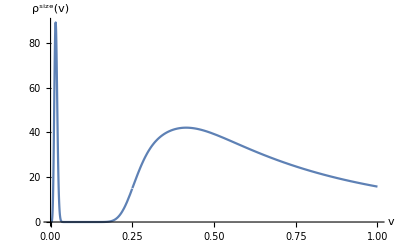

```mathematica
Lval=7;
beta=0.001/Lval^2;

analytPlotGenuine=Plot[rhoalld[v,beta],{v,0,1},PlotRange->All,AxesLabel->{Style["v",16],Style["ρ^size(v)",16]}]
```

## 2. Numerical simulations

```mathematica
Quit[];
```

### Parameters and Functions

```mathematica
(*Parameters*)
Clear[sym,z,w,beta];
L=7; (*N*)
sampnum=100; (*Number of sampling*)
beta=0.001/L^2;(*betabar=0.001*)
dev=Sqrt[2 beta]; (*associated standard deviation*)
cut=10^(-7); (*truncation to extract real eigenvalues-vectors*)

(* Function giving the appropriate multiplicative factor for the different independent entries of the tensor of order 3*)
sym[i_]:=Which[i[[1]]==i[[2]]==i[[3]],1,i[[1]]==i[[2]]||i[[2]]==i[[3]]||i[[3]]==i[[1]],3,True,6];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/nicolas/Documents/GitHub/EdgeRandomTensors

### Data generation: Genuine distribution

```mathematica
Clear[z,w];

(*Genuine Case*)
filenameGenuine=StringJoin["genuineL",ToString[L],"samp",ToString[sampnum],"bb0001.m"];

w=Table[z[i],{i,1,L}];

time1=AbsoluteTime[];

list={};

listtest={};

SetSharedVariable[list,listtest];

ParallelDo[c=Table[0,{L},{L},{L}];
Do[c[[i,j,k]]=Sqrt[sym[{i,j,k}]] RandomVariate[NormalDistribution[0,1]],{i,1,L},{j,i,L},{k,j,L}];
c=Normal[Symmetrize[c]];
devvec=RandomVariate[NormalDistribution[0,dev],L];
eqs=w-c.w.w-devvec;
wsol=NSolve[eqs==0,w];
AppendTo[listtest,Length[wsol]];
Do[w0=w/. wsol[[solnum]];
If[Im[w0].Im[w0]<cut&&Re[w0].Re[w0]>cut,AppendTo[list,{Sqrt[Re[w0].Re[w0]],1}]],{solnum,1,Length[wsol]}];,{sampnum}];

time2=AbsoluteTime[];
Print["time=",time2-time1];
```

time=25.41094

```mathematica
Export[filenameGenuine,list];
```

### Data generation: Signed distribution

```mathematica
Clear[z,w];

(*Signed Case*)
filenameSigned=StringJoin["signedL",ToString[L],"samp",ToString[sampnum],"bb0001.m"];

w=Table[z[i],{i,1,L}];

time1=AbsoluteTime[];

list={};

listtest={};

SetSharedVariable[list,listtest];

ParallelDo[c=Table[0,{L},{L},{L}];
Do[c[[i,j,k]]=Sqrt[sym[{i,j,k}]] RandomVariate[NormalDistribution[0,1]],{i,1,L},{j,i,L},{k,j,L}];
c=Normal[Symmetrize[c]];
devvec=RandomVariate[NormalDistribution[0,dev],L];
eqs=w-c.w.w-devvec;
wsol=NSolve[eqs==0,w];
AppendTo[listtest,Length[wsol]];
mat=IdentityMatrix[L]-2 c.w;
Do[w0=w/. wsol[[solnum]];
If[Im[w0].Im[w0]<cut&&Re[w0].Re[w0]>cut,
mat0=mat/. wsol[[solnum]];
vert1=Sign[Re@Det[mat0]];
AppendTo[list,{Re@Sqrt[w0.w0],vert1}]],{solnum,1,Length[wsol]}];,{sampnum}];

time2=AbsoluteTime[];
Print["time=",time2-time1];

Export[filenameSigned,list];
```

time=19.81414

### Data analysis: Genuine distribution

```mathematica
filename=filenameGenuine;
```

```mathematica
list=Import[NotebookDirectory[]<>filename];
(* Analysis of data *)

wmax=10; (* The range of |v| to see *)
dw=.05; (* Bin size *)

binmax=Ceiling[wmax/dw];

histo=Table[0,{binmax}];

Do[
vert=Ceiling[list[[datnum,1]]/dw];

If[vert<=binmax,

kval=list[[datnum,2]];

histo[[vert]]+=kval;

];

,{datnum,1,Length[list]}];

histo=Table[Around[histo[[i]],Sqrt[histo[[i]]]],{i,1,Length[histo]}];

histo/=sampnum;

newhisto=Table[{dw(i-1/2),histo[[i]]/dw},{i,1,Length[histo]}];
```

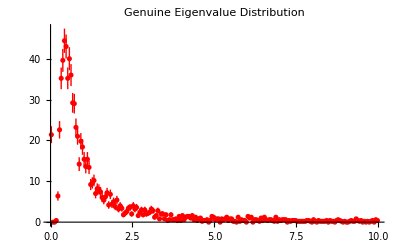

```mathematica
histoPlotGenuine=ListPlot[Map[{1,1}*# &,newhisto],PlotRange->All,PlotStyle->Red,PlotLabel->"Genuine Eigenvalue Distribution"]
```

### Data analysis: Signed distribution

```mathematica
filename=filenameSigned;
```

```mathematica
list=Import[NotebookDirectory[]<>filename];
(* Analysis of data *)

wmax=8; (* The range of |v| to see *)
dw=.05; (* Bin size *)

binmax=Ceiling[wmax/dw];

histop=Table[0,{binmax}];
histom=Table[0,{binmax}];
```

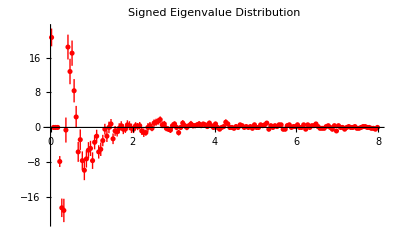

```mathematica
Do[
vert=Ceiling[list[[datnum,1]]/dw];
If[vert<=binmax,

kval=list[[datnum,2]];

Which[kval>0,histop[[vert]]+=1,True,histom[[vert]]+=1];

];

,{datnum,1,Length[list]}];

histo=Table[Around[histop[[i]]-histom[[i]],Sqrt[histop[[i]]+histom[[i]]]],{i,1,Length[histop]}];

histo/=sampnum;

newhisto=Table[{dw(i-1/2),histo[[i]]/dw},{i,1,Length[histo]}];

histoPlotSigned=ListPlot[Map[{1,1}*# &,newhisto],PlotRange->All,PlotStyle->Red,PlotLabel->"Signed Eigenvalue Distribution"]
```

## 3. Plots: Analytics and numerics

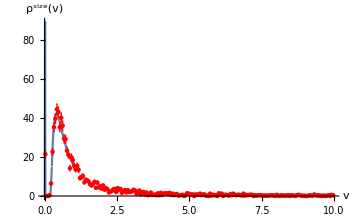

```mathematica
Show[analytPlotGenuine,histoPlotGenuine]
```

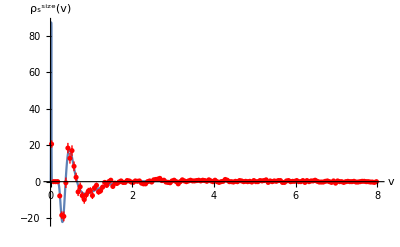

```mathematica
Show[analytPlotSigned,histoPlotSigned]
```

## 4. Lefschetz thimbles (optional)

How did the contour for x=2 was obtained?

## 5. Appendix B

```mathematica
Quit[]
```

```mathematica
Lval=10; (* N *)

maxpoint=6;(* The number of solutions: \int dv rho =1/2,...,maxpoint-1/2 are found *)

(* The range of betabar and its step *)
betabarmin=.01;
betabarmax=.1;
betabardel=.01;

(* Adjustable parameter *)
dv=.001; (* The accuracy of the location of the solution v to the equation *)
vmax=1; (* The range of search; Only the solutions below vmax are found *)

(********************* The part taken from Auffinger et al. *********************)

Clear[p,v,g,s,f,aln];

al=1/2; (* The default value; cannot be changed *)
q=3; (* The order of tensor *)

p[j_,v_]:=(2^j j! Sqrt[Pi])^(-1/2) HermiteH[j,v] Exp[-v^2/2];

g[n_]:=1/2(-Integrate[p[n,t],{t,v,Infinity},Assumptions->v>0]+Integrate[p[n,t],{t,-Infinity,v},Assumptions->v>0]);

s[n_]:=Sum[p[i,v]^2,{i,0,n-1}];

aln[n_]:=Which[Mod[n,2]==0,0,True,
m=(n-1)/2;
p[2m,v]/Integrate[p[2m,t],{t,-Infinity,Infinity}]
]

f[n_]:=(s[n]+(n/2)^(1/2) p[n-1,v] g[n]+aln[n])/Sqrt[n];

Clear[rhod];

rhod[n_]:=2 Sqrt[n]/v^2(q-1)^((n-1)/2) Exp[-(q-2)/(4 (q-1) v^2)] (f[n]/. v->-y*Sqrt[3/(2*2)]/. y->1/v);


(********************* Z_parallel *********************)

Clear[gam1,gam2,gam3,L];

q11=Sqrt[4x-1]/(2 Sqrt[eps] x)-1/(2x);
q12=-1/(2x)+Sqrt[eps]/(2 x Sqrt[4x-1]);
q21=q12;
q22=-Sqrt[eps]Sqrt[4x-1]/(2x)+eps/(2x);

intz2=Limit[(eps-gam3 (L-1) q22 )(1+gam3 (L-1) q11)+(gam1-(L-1) gam3 q12+Sqrt[2 gam2 ]y)^2,eps->0];

q11=(1-Sqrt[1-4x])/(2 x Sqrt[1-4x]);
q12=(1-Sqrt[1-4x]-4x)/(2x Sqrt[1-4x]);
q21=q12;
q22=0;

intz1=Limit[(eps-gam3 (L-1) q22 )(1+gam3 (L-1) q11)+(gam1-(L-1) gam3 q12+Sqrt[2 gam2 ]y)^2,eps->0];

intz1=Simplify[intz1 /. x->(L-1) v^2 / 3 /al ];

intz2=Simplify[intz2 /. x->(L-1) v^2 / 3 /al ];

gam1=(v^4-4 al be)/(v^4+4 al be);
gam2=8 be v^2/(v^4+4 al be);
gam3=8 be v^2/(v^4+12 al be);

Clear[nintz1,nintz2,zpara];

nintz1[v_,be_,L_]=intz1 ;
nintz2[v_,be_,L_]=intz2 ;

zpara[v_,be_,L_]:=1/Sqrt[Pi]*
Which[(L-1)v^2/(3 al)>1/4, NIntegrate[Exp[-y^2] Sqrt[nintz2[v,be,L]],{y,-Infinity,Infinity}],
True,NIntegrate[Exp[-y^2] Sqrt[nintz1[v,be,L]],{y,-Infinity,Infinity}]];


(******************** rho ******************)

Clear[rhoalld,rhoalld1];

rhoalld1[v_,be_]=Expand[Simplify[rhod[Lval]*(v^4/(v^4 +4 al be ))^(1/2) ( v^4/(v^4 +12al be ))^((Lval-1)/2) Exp[- al v^2/(v^4+4 al be)+al /v^2],Assumptions->v>0]];

rhoalld[v_,be_]:= zpara[v,be,Lval]*rhoalld1[v,be]; 


(********************* Routine for finding solutions *********************)

res=Table[

vert=0;
v=dv/2;
intdat={};

Until[

vert>maxpoint-1/2 || v>vmax,

vert+=rhoalld[v,betabar/Lval^2]*dv;

AppendTo[intdat,{v+dv/2,vert}];

v+=dv;
];

If[v>=vmax,maxdata=intdat[[-1,2]],maxdata=maxpoint];

vert=Table[

i=1;

Until[
intdat[[i,2]]>val || i>Length[intdat],
i+=1;
];

i-=1;

v1=val-intdat[[i,2]];
v2=intdat[[i+1,2]]-val;

loc=(v1*intdat[[i+1,1]]+v2*intdat[[i,1]])/(v1+v2),{val,1/2,maxdata,1}];

{betabar,vert}


,{betabar,betabarmin,betabarmax,betabardel}];

Print["Solution list generated"]
```

General::munfl: Exp[-1.5×10^6]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

NIntegrate::slwcon: 数値積分の収束が遅すぎます．特異性がある，積分の値がゼロ，被積分関数が激しく振動する，あるいはWorkingPrecisionが小さすぎるのいずれかが原因である可能性があります．

General::stop: この計算中に，NIntegrate::slwconのこれ以上の出力は表示されません．

Solution list generated

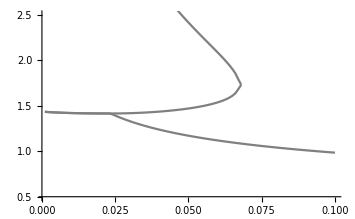
```mathematica
(************* Plotting solutions in terms of y **************)

plotdata=Select[Table[{res[[i,1]],Sqrt[3 al /(2Lval)]/res[[i,2]]},{i,1,Length[res]}],#[[1]]>0 &];

g1=ListPlot[Table[{plotdata[[i,1]],plotdata[[i,2,j]]},{j,1,Length[plotdata[[1,2]]]},{i,1,Length[plotdata]}],PlotLabel->"N="<>ToString[Lval],AxesLabel->{,}];


Show[-Graphics-,g1,PlotRange->{0,2.5},PlotLabel->"N="<>ToString[Lval]]
```

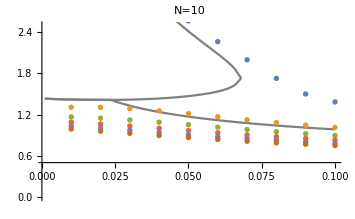

## Extra